# MWE : Creating a closed curve based on given points

## Creating the boundary shape

Here are some points that will form the basis for a closed curve and the polygon passing through those points:

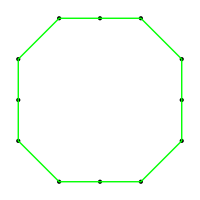

```mathematica
points={{2,-1},{2,0},{2,1},{1,2},{0,2},{-1,2},{-2,1},{-2,0},{-2,-1},{-1,-2},{0,-2},{1,-2}};
Graphics[{PointSize[Large],Point/@points,Green,Line[Append[points,points[[1]]]]},ImageSize->200]
```

Here is a smooth curve that approximates those points

```mathematica
curve=Graphics[{BSplineCurve[points,SplineClosed->True]},ImageSize->200]
```

-Graphics-

The Documentation Center entry for BSplineCurve has an example explaining how to ensure that your spline passes through the given points.

## Creating the filled-in shape

We can replace our BSplineCurve with a BSplineFunction, and use ParametricPlot to graph it with the dummy variable t ranging from 0≤t≤1.

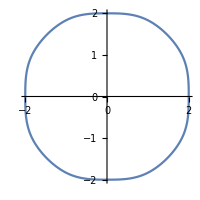

```mathematica
curve=ParametricPlot[BSplineFunction[points,SplineClosed->True][t],{t,0,1},ImageSize->200]
```

We can create a BoundaryMeshRegion from the resulting curve.

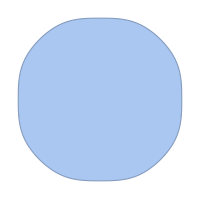

```mathematica
shape=BoundaryDiscretizeGraphics[curve];
Show[shape,ImageSize->200]
```

We can pull out the polygon that was formed by using MeshPrimitives.

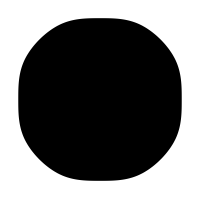

```mathematica
polygon=MeshPrimitives[shape,2];
Graphics[polygon,ImageSize->200]
```